```mathematica
(* Пример того как сохранять результаты в файл. *)
```

```mathematica
(* Сначала зададим, что данные будут сохраняться в том же каталоге, что и notebook (.nb) файл. По умолчанию, файлы сохранаются в каталоге %USERPROFILE%\Document (для Windows). Узнать в какой именно каталог будут сохраняться данные можно вызвав функцию Directory[].*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* Определим функцию, которую будем использовать для создания данных. *)
```

```mathematica
f1[a_]:=Sin[a x+Pi/4]
```

```mathematica
(* График.

Хотя график можно сохранить просто наведя курсор мыши на рисунок и вызвав контекстное меню по правой кнопке, а там --- выбрав "Save Graphic As...", более удобным кажется "программисткий" способ сохранения. *)
```

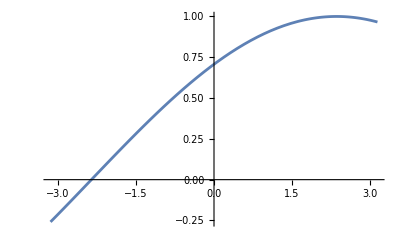

```mathematica
fig=Plot[f1[1/3],{x,-Pi,Pi}]
```

```mathematica
(* Рисунок будет сохранён в файл fig1.pdf в "текущем" каталоге. *)
```

```mathematica
Export["fig1.pdf",fig];
```

```mathematica
(* Табличные данные.

Запись данных в файл осуществляется той же самой функцией Export, если ей передать в качестве второго параметра "массив" (список).

Поскольку мы хотим сохранить в файл "табличные" данные, по колонкам, то нужно использовать третий параметр с ключевым словом "Table". *)
```

```mathematica
dat=Table[{x,f1[1/3],f1[Sqrt[2.5]]},{x,0.1,0.2,0.01}]
```

{{0.1,0.73028,0.809624},{0.11,0.732553,0.818803},{0.12,0.734818,0.827778},{0.13,0.737075,0.836545},{0.14,0.739323,0.845103},{0.15,0.741564,0.85345},{0.16,0.743796,0.861583},{0.17,0.74602,0.869501},{0.18,0.748235,0.877202},{0.19,0.750443,0.884683},{0.2,0.752642,0.891944}}

```mathematica
Export["data.dat",dat,"Table"];
```

```mathematica
(* В файл, по колонкам были записаны эти данные. Это можно проверить открыв файл data.dat в любом текстовом редакторе. *)
```

```mathematica
(* Если объём генерируемых данных велик, то наверное следует "подавить" вывод на экран (в notebook) поставив в конце команды символ ; *)
```